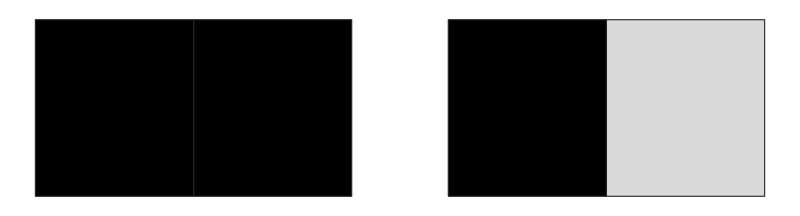

```mathematica
GraphicsRow[Graphics[Flatten[MapIndexed[{EdgeForm[GrayLevel[.15]],GrayLevel[0.85-#1],Rectangle[{First[#2]-1,0}]}&,#]],]&/@{{1,1},{1,0}},]
```